```mathematica
(* get the radius function right *)
```

## Styles and files

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["scpPaperStylings.m"]
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\DraftFigures"}];



getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
(*fig
*)];
```

## Stll worlo

### Next

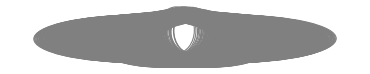

```mathematica
rCircumferenceTransform[r_] := 1/r;xzCircumferenceTransform[xz_,r_] := Module[{x,z},
{x,z}=xz;
x = x * rCircumferenceTransform[r];
{x,z}
];
xzCircumferenceTransform[Disk[xz_,r_]] := Ellipsoid[xzCircumferenceTransform[xz,r],
{rCircumferenceTransform[r],1}];
disks = runDisks[runCone,bareOnly=False];
Graphics[{ffs,Values@Map[xzCircumferenceTransform,disks]}]
```

```mathematica
run=runCone;transform := xzRadiusScalingTransform;
namedPoints = Point /@ runTransformedNodes[run,transform,bareOnly=True];
namedPoints
```

```mathematica
runTransformDisksByCircumference[run_] := Module[{g,disks},
disks =runDisks[run];

disks = Map[doDiskTransformRadius[#,transformRadius]& , disks];
disks
];
```

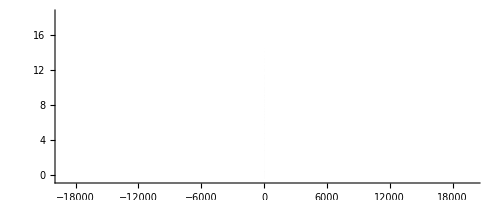

```mathematica
makeCone2DGraphics[run_] := Module[{},


transform := rScalingTransform;
namedPoints = Point /@ runTransformedNodes[run,transform,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,transform];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runTransformedRadiusToDisks[run,transform];
colouredDisks= Association@Map[#->{cylinderNodeColour[namedType[#]],namedDisks[#]}&,Keys[namedDisks]];

Graphics[Values@colouredDisks,PlotRange->All]
];
cone2DShow = makeCone2DGraphics[runCone];
Show[cone2DShow,Axes->True]
```

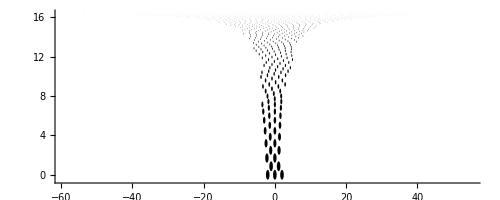

```mathematica
Graphics[{Take[Values[runTransformedToDisks[run,coneTransform2D[stemParameters]]],{1,1000}]},Axes->True]
```

```mathematica
diskTransform[{zMin_,zMax_}] := Module[{f},
f= Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = zMax- z;
r= r/(zMax-zMin); (* outer ring radius 1 *)
r*{Cos[2 π x],Sin [ 2 π x]} 
]
];
f
];
coneTransform2DRadius :=  Module[{f},
f= Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = 1/r;
x = x *r;
{x,z}
]
];
f
];
coneTransform2D[stemParameters_] := Module[{f},
f= Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = stemParameters["cone"]["rFunction"][z];
x = x/rScale;
{x,z}
]
];
f
];
```

```mathematica
diskGraphics[run_,transform_] := Module[{g,g2,lp,nodes,zRange,vMesh,runDiskTransform,colouredNodes},
g=run["ContactGraph"];
nodes=AnnotationValue[g,VertexCoordinates];
diskNodes= transform /@  nodes;
(*vMesh= voronoiMeshNoEdge[nodes,{stemParameters["zUpperRim"],stemParameters["zCutoff"]}];
lp=meshToTransformedGraphics[vMesh,transform];
*)
colouredNodes= Map[{xStyle[nodeType[#]],PointSize[Medium],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

(*contactLines= Last/@Select[graphToContactLines[run],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
diskContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};
*)
g2=Graphics[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],diskContactLines,{FaceForm[White],Disk[{0,0},0.4]},
colouredNodes},Method->{"ShrinkWrap" -> True}];
g2=Graphics[{
colouredNodes}];
g2
];
```

## Cruft

```mathematica
showDiskMeshFromNodes[g_] := Module[{gstyle,nodes,vx,mask},
nodes=AnnotationValue[g,VertexCoordinates];
v=VoronoiMesh[nodes];
v=Region[Style[v,EdgeForm[Black],FaceForm[None]]];
mask= DiscretizeRegion@RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[]];
mask=Region[Style[mask,White]];
gstyle=Graph[g,VertexSize->Large,VertexStyle->Gray];
Show[gstyle,v,mask,PlotRange->{{-1,1},{-1,1}}]
];
```

```mathematica
stackGraphics[run_]:= Module[{disks,diskStyle,contactLines},
disks=Values[Map[#Disk&,run["DiskData"]]];
diskStyle[p:Disk[xz_,r_]] := {xStyle[nodeType[xz]],p};
contactLines= {RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&]};
 Graphics[{ffs,diskStyle/@disks,{contactLines}},PlotRange->{{-1/2,1/2},{4.3,5.1}},PlotRangeClipping->True]
];
```

```mathematica
diskGraphics[run_,transform_] := Module[{g,g2,lp,nodes,zRange,vMesh,runDiskTransform,colouredNodes},
g=run["ContactGraph"];
nodes=AnnotationValue[g,VertexCoordinates];
vMesh= voronoiMeshNoEdge[nodes,{stemParameters["zUpperRim"],stemParameters["zCutoff"]}];
lp=meshToTransformedGraphics[vMesh,transform];

colouredNodes= Map[{xStyle[nodeType[#]],PointSize[Medium],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

contactLines= Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
diskContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};

g2=Graphics[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],diskContactLines,{FaceForm[White],Disk[{0,0},0.4]},
colouredNodes},Method->{"ShrinkWrap" -> True}];
g2
];
```

```mathematica
polygonTransform[Polygon[poly___],transform_] := (Polygon[Map[transform,poly]]);
lineTransform[Line[line___],transform_] := (Line[Map[transform,line]]);
```

```mathematica
ffs= Directive[FaceForm[None],EdgeForm[Gray]];
```

```mathematica
meshToTransformedGraphics[vMesh_,transform_] := Module[{lMesh,lMesh2,lines2,lines3,rmesh,polys2,polys3},
lMesh = MeshRegion[MeshCoordinates[vMesh],MeshCells[vMesh,1]];
lMesh2= DiscretizeRegion[lMesh,MaxCellMeasure->{"Length"->.005}];
lines2= MeshPrimitives[lMesh2,1];
lines3= lineTransform[#,transform]&/@lines2;
rmesh =DiscretizeRegion[vMesh,MaxCellMeasure->{"Length"->.01}];polys2= MeshPrimitives[rmesh,2];
polys3= Map[polygonTransform[#,transform]&,polys2];
<|"Lines"->lines3,"Polygons"->polys3|>
];
```